```mathematica
Clear["Global`*"]
```

We use units [ω]=E_F, [q]=k_F, q_TF=(... r_s)k_F, [χ]=m/a_0

```mathematica
imchi=(√(2m))^d/(2^d π^((d-1)/2)Gamma[(d+1)/2] √ϵq)(HeavisideTheta[1-(ω-ϵq)^2/(4ϵq μ)](μ-(ω-ϵq)^2/(4ϵq))^((d-1)/2)-HeavisideTheta[1-(ω+ϵq)^2/(4ϵq μ)](μ-(ω+ϵq)^2/(4ϵq))^((d-1)/2));
```

```mathematica
reEp=1+qTF^2/q^2(1/2+kF/(4q)((1-(ω-ϵq)^2/(q^2 vF^2))Log@Abs[(ω-vF* q-ϵq)/(ω+vF *q-ϵq)]+(1-(ω+ϵq)^2/(q^2 vF^2))Log@Abs[(ω+vF* q+ϵq)/(ω-vF *q+ϵq)]));
imEp=Piecewise[{{π/2*ω/(vF q)*qTF^2/q^2,ω≤vF q-ϵq&&q<2kF},{(π kF)/(4q)*qTF^2/q^2(1-(ω-ϵq)^2/(q^2 vF^2)),vF q-ϵq≤ω≤ϵq+vF q&&q<2kF},{(π kF)/(4q)*qTF^2/q^2(1-(ω-ϵq)^2/(q^2 vF^2)),ϵq-vF q≤ω≤ϵq+vF q&&q≥2kF}},0];
```

```mathematica
exprsubs={ϵq->q^2/(2m),vF->kF/m};
unitsubs={ω->ω*(kF^2/(2m)),q->q*kF};
kqsubs={kF->((9π)/4)^(1/3)*1/rs*1/a0,qTF->(1/9((9π)/4)^(2/3)rs)^(-1/2)1/a0};
subs[x_]:=Simplify[x/.exprsubs/.unitsubs/.kqsubs,{a0>0,m>0,rs>0,q>0}];
```

```mathematica
reϵ[q_,ω_,rs_]:=Evaluate[subs[reEp]]
imϵ[q_,ω_,rs_]:=Evaluate[subs[imEp]]
```

```mathematica
Manipulate[
pReIm=Plot[{reϵ[0.2,ω,rs],imϵ[0.2,ω,rs]},{ω,0,2},PlotRange->All,PlotPoints->500];
pPole=Plot[{-10^3 Im[1/(reϵ[0.2,ω,rs]+I*(0.00001+imϵ[0.2,ω,rs]))]},{ω,0,2},Filling->{Bottom},PlotRange->{Automatic,{0,60}},PlotStyle->Darker@Green,PlotPoints->500];
Show[pReIm,pPole],
{rs,0,20}]
```

```mathematica
{FindRoot[reϵ[0.2,ω,3],{ω,0.3}],FindRoot[reϵ[0.2,ω,3],{ω,1.5}]}
```

{{ω→0.3316},{ω→1.65894}}

## Fridel oscillation

We use units [Veff]=e^2/ϵ_0 k_F, [r]=k_F^-1

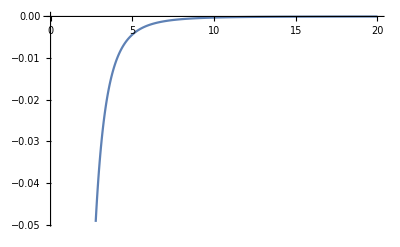

```mathematica
Plot[{1/reϵ[q,0,3]-1},{q,0,20},PlotPoints->500]
```

```mathematica
VYuk[r_]:=Evaluate[Exp[-qTF r/kF]/(4π r)/.kqsubs/.rs->3]
```

```mathematica
Veff0[r_]:=Evaluate[1/(2 π^2)*1/r Integrate[1/q^2*q Sin[q r],{q,0,∞},Assumptions->r>0]];
Veff[r_]:=1/(2 π^2)*1/r NIntegrate[1/q^2*(1/reϵ[q,0,3]-1)*q Sin[q r],{q,0,20}]+Veff0[r];
```

```mathematica
data=Module[{rdata,Vdata},
rdata={Array[#&,300,{0.01,4}],Array[#&,300,{4.01,20}]}//Flatten;
Vdata=Veff/@rdata;
{rdata,Vdata}//Transpose
];
```

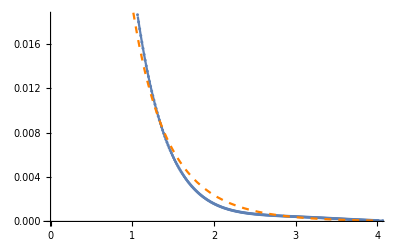

```mathematica
p1=ListLinePlot[data,PlotMarkers->{Automatic, 3},PlotRange->{{0,4},Automatic}];
p2=Plot[VYuk[r],{r,0.001,4},PlotStyle->{Dashed,Orange}];
Show[p1,p2]
```

```mathematica
VFriedel=NonlinearModelFit[Select[data,#[[1]]>5&],a Cos[2 r]/r^3,{a},r]
```

FittedModel[(0.00612814 Cos[2 r])/r^3]

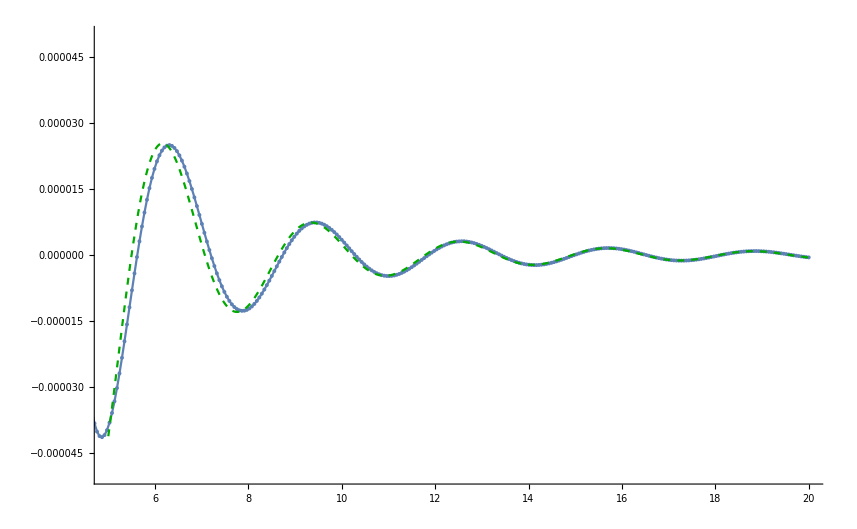

```mathematica
p3=ListLinePlot[data,PlotMarkers->{Automatic, 4}];
p4=Plot[VFriedel[r],{r,5,20},PlotStyle->{Dashed,Darker@Green},PlotRange->All];
Show[p3,p4,PlotRange->{{5,20},{-10^-4/2,10^-4/2}}]
```